```mathematica
ClearAll["Global`*"]
```

## Step response

### TF function

```mathematica
maxt = 0.5;
k = 10;
T3 = 0.08;
T4 = 0.04;
TFstep=Simplify[OutputResponse[k/((T3*s + 1)(T4 *s +1))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic,UnitStep[t],t]];
TFstepf[t_]=TFstep;
TFstableValue=Limit[TFstep,t->Infinity][[1]];
dashingStyle = Dashing[{maxt/25,maxt/25-maxt/75}];
```

### Horizontal Dashed Line

```mathematica
stepLineAbove=Line[{{0,TFstableValue},{maxt,TFstableValue}}];
```

### Tangent Line

```mathematica
a=(T3*T4)/(T3-T4)*Log[T3/T4];
tangentLine =(D[TFstep,t]/.t->a)×(t-a) + (TFstep/.t->a);
```

### Vertical Dashed Line

```mathematica
sl=Solve[tangentLine==TFstep];
tangientInStable=sl[[All,1,2]][[1]];
vertLine=Line[{{tangientInStable,0},{tangientInStable,TFstableValue}}];
ss=Solve[tangentLine==TFstableValue];
tangientInStable=ss[[All,1,2]][[1]];
vertLine2=Line[{{tangientInStable,0},{tangientInStable,TFstableValue}}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

### Sizes

#### Common

```mathematica
arrowsHeads=Arrowheads[{-.035,.035}];
sizeText[text_]:=Style[text, 18,FontSlant->Italic,FontFamily->"Times New Roman"];
```

#### Vertical size

```mathematica
verSizeText=Text[
sizeText["k"],
{
-0.008,
TFstableValue
}
];
```

### Plot

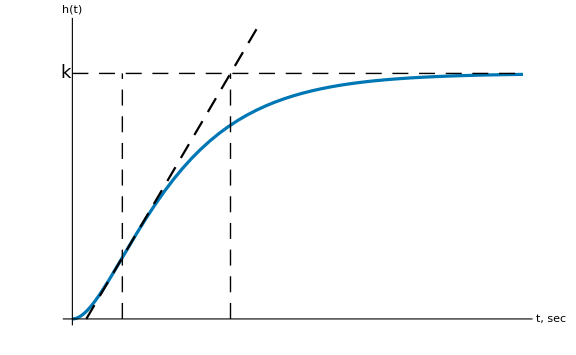

```mathematica
tickXStep = 1/10;
tickYStep = 2;
stepRespPic=Plot[{TFstep, tangentLine},{t, 0, maxt},
AxesStyle->Directive[Black, FontSize->9],
AxesLabel->{sizeText["t, sec"], sizeText["h(t)"]},
GridLines->None,
PlotStyle->{{RGBColor["#0077b5"],Thickness[0.004]},{Black,dashingStyle}},
PlotRange->{{0,maxt},{0,TFstableValue*1.2}},
PlotRangeClipping->False,
ImageSize->Large,
Ticks->{(#&@Array[{tickXStep #,}&,100]),(#&@Array[{tickYStep #,}&,100])},
Epilog->{
{Directive[Black,dashingStyle],stepLineAbove},
{Directive[Black,dashingStyle],vertLine},
{Directive[Black,dashingStyle],vertLine2},
{verSizeText}
}
]
```

```mathematica
Export["step.png",stepRespPic,ImageResolution->900];
```